```mathematica
PDF[BinomialDistribution[10,0.5],x]
```

Piecewise[{{0.000976563 Binomial[10,x], 0≤x≤10}, {0, True}}]

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->40}];
```

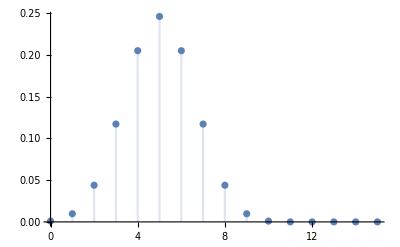

```mathematica
DiscretePlot[Piecewise[{{0.0009765625 Binomial[10,x],0≤x≤10}},0],{x,0,15}]
```

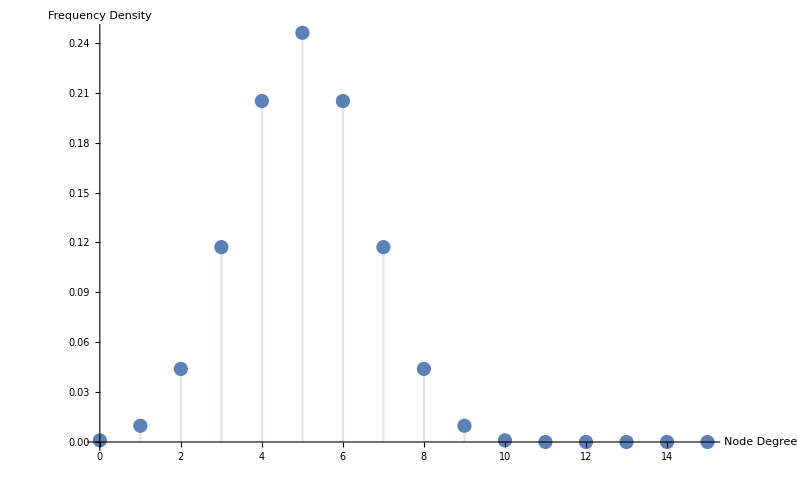

```mathematica
Show[%26,AxesLabel->{HoldForm["Node Degree"],HoldForm[Frequency Density]},PlotLabel->None,LabelStyle->{24,GrayLevel[0]}]
```

```mathematica
Show[%26,PlotLabel->None,LabelStyle->{24,GrayLevel[0]}]
```

```mathematica
PDF[BinomialDistribution[59,0.2],x]
```

Piecewise[{{0.2^x 0.8^(59-x) Binomial[59,x], 0≤x≤59}, {0, True}}]

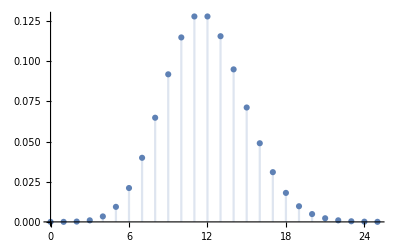

```mathematica
DiscretePlot[Piecewise[{{0.2^x 0.8^(59-x) Binomial[59,x],0≤x≤59}},0],{x,0,25}]
```

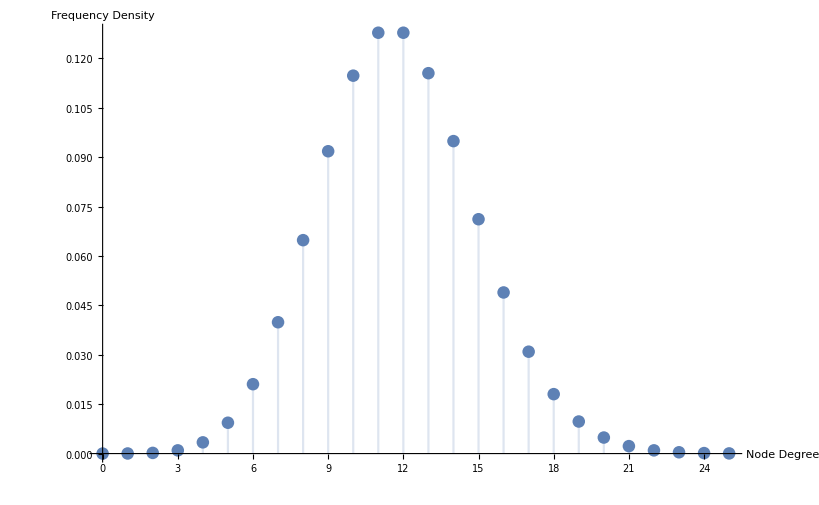

```mathematica
Show[%31,AxesLabel->{HoldForm["Node Degree"],HoldForm[Frequency Density]},PlotLabel->None,LabelStyle->{24,GrayLevel[0]}]
```

```mathematica
PDF[BinomialDistribution[70,0.02],x]
```

Piecewise[{{0.02^x 0.98^(70-x) Binomial[70,x], 0≤x≤70}, {0, True}}]

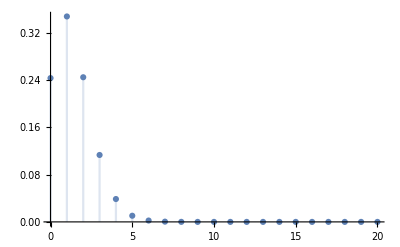

```mathematica
DiscretePlot[Piecewise[{{0.02^x 0.98^(70-x) Binomial[70,x],0≤x≤70}},0],{x,0,20}]
```

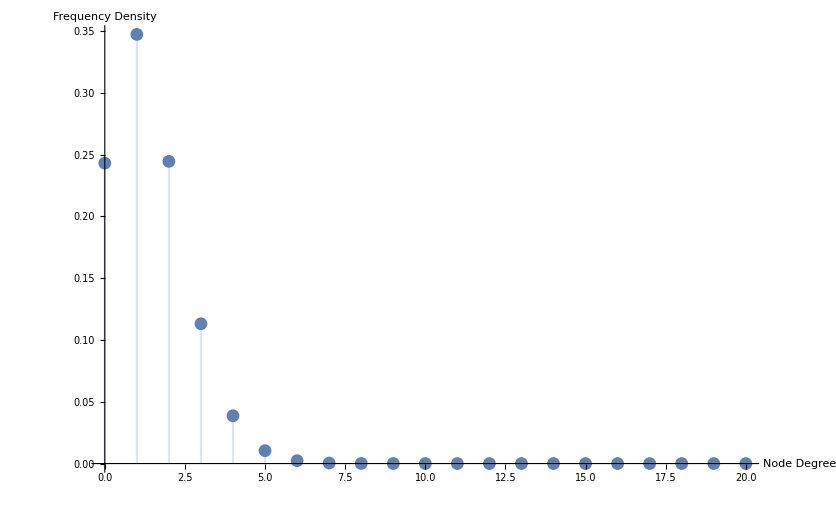

```mathematica
Show[%33,AxesLabel->{HoldForm["Node Degree"],HoldForm[Frequency Density]},PlotLabel->None,LabelStyle->{24,GrayLevel[0]}]
```

```mathematica
BarabasiAlbertGraphDistribution[500,0.5]
```

```mathematica
BarabasiAlbertGraphDistribution[700,5]
```

BarabasiAlbertGraphDistribution[500,5]

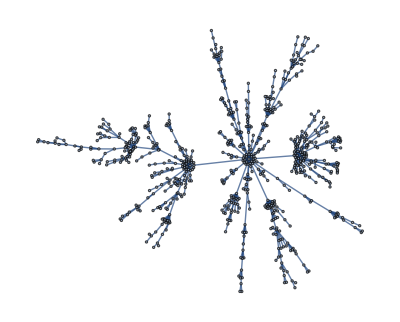

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[700,1]]
```

```mathematica
VertexDegree[%35]
```

{2,37,1,43,16,44,4,10,5,3,21,3,4,9,4,1,3,5,9,5,6,8,5,10,11,6,12,6,2,1,1,6,5,23,9,1,3,2,5,5,5,3,2,1,3,2,4,10,6,1,1,1,3,5,4,1,3,15,1,1,2,1,5,3,5,1,2,3,1,2,1,2,4,2,1,1,4,4,1,1,1,4,9,2,11,1,6,1,1,1,1,1,3,2,2,2,1,4,1,3,2,3,1,4,8,1,3,3,2,1,1,1,7,7,5,1,1,3,7,6,3,3,3,4,1,1,2,3,2,1,3,1,1,3,6,4,5,1,2,1,5,2,6,1,7,1,1,4,6,1,1,1,1,1,2,2,3,2,1,1,1,1,1,5,1,1,2,1,1,3,2,1,2,2,1,1,1,2,1,2,1,3,2,2,2,1,2,2,1,2,3,1,2,2,1,1,3,2,2,1,1,2,1,1,1,2,1,1,1,3,1,2,1,1,1,3,1,2,2,1,5,1,1,1,1,2,1,2,1,2,1,2,1,3,1,2,1,3,1,1,1,1,2,1,1,3,1,1,2,2,2,2,1,1,2,1,1,1,2,1,1,1,1,2,2,1,1,1,1,2,2,2,1,2,1,1,1,1,1,1,1,1,1,5,1,4,3,1,4,1,1,2,1,2,1,3,2,1,1,3,2,2,1,2,1,2,1,4,1,2,1,1,1,1,1,4,1,2,1,1,1,3,1,1,2,1,1,1,1,1,2,3,1,1,2,1,1,1,1,1,2,1,2,1,1,1,1,1,1,3,1,2,1,2,1,1,1,1,1,1,1,1,1,3,1,1,1,1,2,1,1,1,1,1,1,1,2,2,1,3,2,1,2,1,1,1,1,1,1,2,1,1,1,1,2,2,1,2,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,4,1,2,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

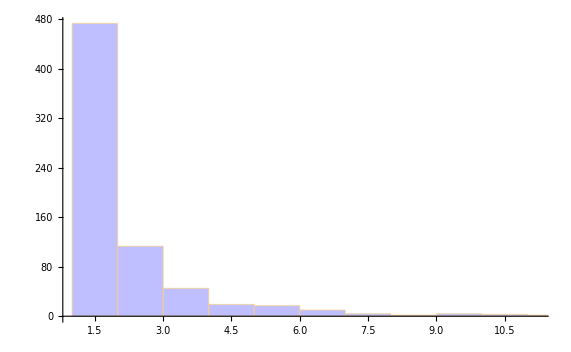

```mathematica
Histogram[%36,ChartStyle->{Opacity[.25,Blue]}]
```